# Tutorial

## Basics

Based on online tutorial: https://www.youtube.com/watch?v=mXFDAz3S9Uk&list=PLxdnSsBqCrrE4j99TtW_zdyED2IVgbBUd&index=1

## Basics

Storing variables:

```mathematica
x=3
```

3

Showing how ; suppresses output

```mathematica
y=4;
z=x+y
```

7

Mathematica can deal with exact fractions

```mathematica
f=5/2+2*t
```

5/2+2 t

There is a difference between exact inputs and decimal inputs

```mathematica
f2=2.5+2*t
```

2.5+2 t

Demonstrate use of comments in code cell

```mathematica
(*Here's a comment*)
dog=4;
cat=5/u+6.5;

(*now create a goat from a cat and a dog*)
goat=dog+cat+750
```

760.5+5/u

## Typesetting

This is a sentence in the "Text" format

```mathematica
(*This is a sentence in the "Code" format*)
```

```mathematica
(*This is a sentence in the "Input" format, which is a bit more general purpose and can be later toggled to "Text" or "Code"*)
```

## Greek Letters

Consider the polynomial:
αx^2+βx+γ=0
Another way to type these out is using the esc key:
(∂x)/(∂y)=2

## Built-in Functions

```mathematica
x=2
```

2

```mathematica
Clear[x]
x
```

x

Now x is undefined again

```mathematica
Sin[π]
```

0

```mathematica
Sin[45*π/180]
Sin[45.0*π/180]
```

1/(√2)

0.707107

```mathematica
Solve[a x^2+b x+c==0,x]
(*In LaTeX*)
Solve[,x]
```

{{x→(-5/68+(3 ⅈ)/68) (b-√(b^2-(20+12 ⅈ) c))},{x→(-5/68+(3 ⅈ)/68) (b+√(b^2-(20+12 ⅈ) c))}}

{{x→(-5/68+(3 ⅈ)/68) (b-√(b^2-(20+12 ⅈ) c))},{x→(-5/68+(3 ⅈ)/68) (b+√(b^2-(20+12 ⅈ) c))}}

```mathematica
Print["Hello World"]
```

Hello World

## Matrices

## Matrix Definitions

Define matrices using lists:

```mathematica
A={{1,2,3},{4,5,6},{7,8,9}};
MatrixForm[A]
```

(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)

Define matrices using built-in matrix notation

```mathematica
A=({{1, 2, 3}, {4, 5, 6}, {7, 8, 9}});
A // MatrixForm
```

(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)

MatrixForm is only used to display matrices and cannot be used to manipulate them

```mathematica
Subscript[B, 1]=MatrixForm[A]
Subscript[B, 2]=MatrixForm[A]
Subscript[B, 1]+A
```

(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)

(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)

{{1+(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9),2+(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9),3+(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)},{4+(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9),5+(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9),6+(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)},{7+(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9),8+(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9),9+(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)}}

```mathematica
A+A // MatrixForm
```

(2 | 4 | 6
8 | 10 | 12
14 | 16 | 18)

## Matrix Operations

#### Dot product

Use Dot[] or .

```mathematica
Clear[{a,b,c,d,e,f,g,h}]
A=({{a, b}, {c, d}});
B=({{e, f}, {g, h}});
Print[A // MatrixForm, ".", B // MatrixForm]
Dot[A,B] // MatrixForm
A.B // MatrixForm
```

(a | b
c | d).(e | f
g | h)

(a e+b g | a f+b h
c e+d g | c f+d h)

(a e+b g | a f+b h
c e+d g | c f+d h)

#### Element-wise multiplication

```mathematica
A=({{1, 2, 3}, {4, 5, 6}});
B=({{1, 2, 3}, {4, 5, 6}});
A*B // MatrixForm
```

(1 | 4 | 9
16 | 25 | 36)

#### Matrix Powers

```mathematica
A=({{1, 2}, {3, 4}})

A^2 // MatrixForm
A^2 // MatrixForm
A*A // MatrixForm

A.A.A // MatrixForm
MatrixPower[A,3] // MatrixForm
```

{{1,2},{3,4}}

(1 | 4
9 | 16)

(1 | 4
9 | 16)

(1 | 4
9 | 16)

(37 | 54
81 | 118)

(37 | 54
81 | 118)

#### Submatrices

```mathematica
A // MatrixForm
Part[A, 2, 1] (*Retrieves the element at row 2, col 1*)
A[[2, 1]]

{A[[2, All]]} // MatrixForm (*Retrieves row 2 of the A*)
A[[All, 2]] // MatrixForm
```

(1 | 2
3 | 4)

3

3

(3 | 4)

(2
4)

#### Concatenating Matrices

```mathematica
row1 = ({{1, 2, 3}});
row2 = ({{4, 5, 6}});
Join[row1, row2] // MatrixForm

Transpose[Join[Transpose[row1], Transpose[row2]]] // MatrixForm
```

(1 | 2 | 3
4 | 5 | 6)

(1 | 2 | 3 | 4 | 5 | 6)

## 2D Plotting

Tutorial: https://www.youtube.com/watch?v=j-utznrXmcY&list=PLxdnSsBqCrrE4j99TtW_zdyED2IVgbBUd&index=3

## Plot

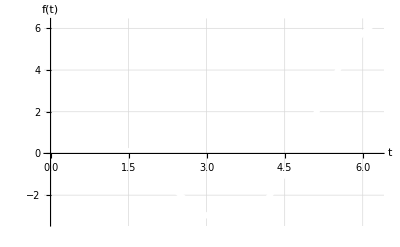

```mathematica
plot1 = Plot[t*Cos[t], {t, 0, 2π},
AxesLabel->{"t","f(t)"},
PlotLabel->"",
GridLines->Automatic,
PlotStyle->{White, Thickness[0.01]}
]
```

## Show

```mathematica
plot2 = Plot[t*Cos[t], {t, 0, 2π},
AxesLabel->{"t","f(t)"},
PlotLabel->"",
GridLines->Automatic,
PlotStyle->{White, Thickness[0.01]}
]
```

-Graphics-

Too lazy to continue this, watch the tutorial video instead

## 3D Plotting

## Plot

```mathematica
plotSurface = Plot3D[x^2+y^2,{x, -10, 10}, {y, -10, 10},
AxesLabel->{"x", "y", "f(x,y)"},
PlotLabel->"Title",
ColorFunction->Hue,
PlotStyle->Opacity[0.25],
(*FaceGrids->All,*)
ViewPoint->{0, -∞, 0}
]
```

-Graphics3D-

## ParametricPlot3D

```mathematica
Subscript[f, x]=t Cos[t]
Subscript[f, y]=t Sin[t]
Subscript[f, z]=(Subscript[f, x]^2+Subscript[f, y]^2)

plotLine = ParametricPlot3D[{Subscript[f, x],Subscript[f, y],Subscript[f, z]},{t, 0, 2π},
AxesLabel->{"x","y","z"}
]
```

t Cos[t]

t Sin[t]

t^2 Cos[t]^2+t^2 Sin[t]^2

-Graphics3D-

```mathematica
Show[plotLine,plotSurface,
PlotRange->{{-10, 10},{-10,10},{-5, 100}}
]
```

-Graphics3D-

## Point

```mathematica
P=({{1, 2, 3}});
P // MatrixForm
pt = Point[P];
plotPoint = Graphics3D[
{AbsolutePointSize[10], Green, pt}
]
```

(1 | 2 | 3)

-Graphics3D-

```mathematica
Show[plotLine,plotSurface,plotPoint]
```

-Graphics3D-

## Animations

## Simple Animations

Consider a simple function
f (t) = Asin (ωt)

```mathematica
Clear[A, ω, t, f];
f[t_,A_,ω_]=A Sin[ω t];
```

Make a simple static plot

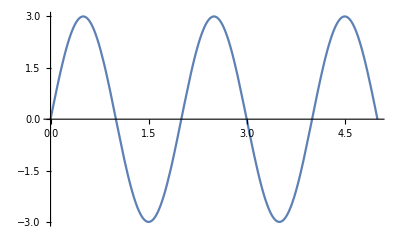

```mathematica
AExample = 3;
ωExample = π;

Plot[f[t, AExample, ωExample], {t, 0, 5}]
```

```mathematica
AExample = 3;
ωExample = π;

Manipulate[
	Plot[f[t, A, ω], 
	{t, 0, 5},
	AxesLabel->{"t", "f(t)"}
	], 
	{ω, 2, 4},
	{A, 1, 4}
]
```

## Animation Theory

Watch until 10:05: https://www.youtube.com/watch?v=3I1_5M7Okqo

## Animation

```mathematica
Clear[t, x, y, z]
x[t_]=5 Cos[t];
y[t_]=2 Sin[t];
z[t_]=t;

ParametricPlot3D[{x[t],y[t],z[t]},{t, 0, 2π},
AxesLabel->{"x", "y", "z"},
PlotLabel->"Testing"
]
```

-Graphics3D-

```mathematica
tRange=Range[0,2π,(2π)/99]; (*Create 100 time steps*)
```

Define/initialize a container that will hold the frames of the animation

```mathematica
movieVector = ConstantArray[0, Length[tRange]];
```

Use a ‘for’ loop to create frames of animation

```mathematica
For[k = 1, k ≤ Length[tRange], k++, 
	tk = tRange[[k]];
	xk = x[tk];
	yk = y[tk];
	zk = z[tk];

	movieVector[[k]] = Show[Graphics3D[{AbsolutePointSize[15], Green, Point[{xk, yk, zk}]}],
		ParametricPlot3D[{x[t], y[t], z[t]}, {t, 0, 2 π}],
		AxesLabel -> {"x", "y", "z"},
		PlotLabel->StringJoin["t = ", ToString[N[tk]]]
	]
]
```

Save the movie now

```mathematica
SetDirectory["/Users/ethan/Desktop"];
fileName = "curveMathematica.mp4";
Export[fileName, movieVector];
```

Check where Mathematica stores the file using the “Directory” command

```mathematica
Directory[]
```

/Users/ethan/Desktop

## Graphics

## Using native graphics engine

-Graphics-

## Importing Graphics from an External Source

Pasting an image:

-Graphics-

Pasting a Keynote graphic

## Differentiation and Integration

## Derivatives

```mathematica
f[x_]:=(x-1)^2/(x^2+1)
D[f[x],x]
f'[x]
D[f[x], x]

Simplify[{D[f[x],x], f'[x], D[f[x], x]}]
```

-(2 (-1+x)^2 x)/((1+x^2)^2)+(2 (-1+x))/(1+x^2)

-(2 (-1+x)^2 x)/((1+x^2)^2)+(2 (-1+x))/(1+x^2)

-(2 (-1+x)^2 x)/((1+x^2)^2)+(2 (-1+x))/(1+x^2)

{(2 (-1+x^2))/((1+x^2)^2),(2 (-1+x^2))/((1+x^2)^2),(2 (-1+x^2))/((1+x^2)^2)}

```mathematica
f''[x]
```

(8 (-1+x)^2 x^2)/((1+x^2)^3)-(2 (-1+x)^2)/((1+x^2)^2)-(8 (-1+x) x)/((1+x^2)^2)+2/(1+x^2)

```mathematica
Simplify[(8 (-1+x)^2 x^2)/((1+x^2)^3)-(2 (-1+x)^2)/((1+x^2)^2)-(8 (-1+x) x)/((1+x^2)^2)+2/(1+x^2)]
FullSimplify
```

-(4 x (-3+x^2))/((1+x^2)^3)

FullSimplify

```mathematica
f'[0.5]
f''[0.5]
```

-0.96

2.816

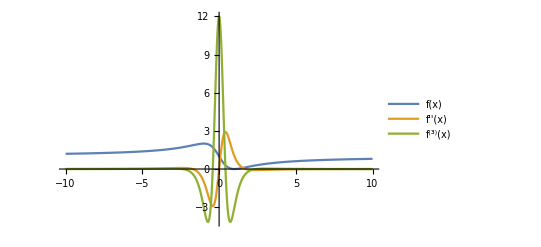

```mathematica
Plot[{f[x],f''[x], f'''[x]},{x, -10, 10}, PlotLegends->"Expressions", PlotRange->All]
```

```mathematica
d10 = D[f[x], {x, 10}]
FullSimplify[d10]
```

(-1+x)^2 ((3715891200 x^10)/((1+x^2)^11)-(8360755200 x^8)/((1+x^2)^10)+(6502809600 x^6)/((1+x^2)^9)-(2032128000 x^4)/((1+x^2)^8)+(217728000 x^2)/((1+x^2)^7)-3628800/((1+x^2)^6))+20 (-1+x) (-(185794560 x^9)/((1+x^2)^10)+(371589120 x^7)/((1+x^2)^9)-(243855360 x^5)/((1+x^2)^8)+(58060800 x^3)/((1+x^2)^7)-(3628800 x)/((1+x^2)^6))+90 ((10321920 x^8)/((1+x^2)^9)-(18063360 x^6)/((1+x^2)^8)+(9676800 x^4)/((1+x^2)^7)-(1612800 x^2)/((1+x^2)^6)+40320/((1+x^2)^5))

-(7257600 x (-11+165 x^2-462 x^4+330 x^6-55 x^8+x^10))/((1+x^2)^11)

## Integrals

```mathematica
g[x_]:=x^2+x^3
Integrate[g[x], x]
∫g[x]ⅆx
Integrate[g[x], {x, 2, 10}]
∫_2^10 g[x]ⅆx
Simplify[∫∫1/((x^2+y^2)^(1/2))ⅆxⅆy]
Simplify[Integrate[1/((x^2+y^2)^(1/2)), x, y]]
value=∫_0^2 ∫_0^2 1/((x^2+y^2)^(1/2))ⅆxⅆy
N[value]
NIntegrate[1/((x^2+y^2)^(1/2)),{x, 0, 2}, {y, 0, 2}]
```

x^3/3+x^4/4

x^3/3+x^4/4

8480/3

8480/3

1/2 (-y Log[1-x/(√(x^2+y^2))]+y Log[1+x/(√(x^2+y^2))]+2 x Log[y+√(x^2+y^2)])

1/2 (-x Log[1-y/(√(x^2+y^2))]+x Log[1+y/(√(x^2+y^2))]+2 y Log[x+√(x^2+y^2)])

1/2 Log[577+408 √2]

3.52549

3.52549

## Solving Equations

```mathematica
f[x]=a x^2 + b x + c == 0

Roots[f[x],x]
Solve[f[x], x]
FindRoot[x^2-1==0, {x, -2}]
Reduce[f[x], x]
```

c+b x+a x^2==0

x==(-b-√(b^2-4 a c))/(2 a)||x==(-b+√(b^2-4 a c))/(2 a)

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

{x→-1.}

(a≠0&&(x==(-b-√(b^2-4 a c))/(2 a)||x==(-b+√(b^2-4 a c))/(2 a)))||(a==0&&b≠0&&x==-c/b)||(c==0&&b==0&&a==0)

## Roots

```mathematica
Roots[x^3+1==0, x]
```

x==-1||x==-(-1)^(2/3)||x==(-1)^(1/3)

```mathematica
Roots[x^3 + 1 == 0, x] // N
```

x==-1.||x==0.5-0.866025 ⅈ||x==0.5+0.866025 ⅈ

```mathematica
NRoots[x^3 + 1== 0, x]
```

x==-1.||x==0.5-0.866025 ⅈ||x==0.5+0.866025 ⅈ

```mathematica
(0.5-0.866025ⅈ)^3
```

-0.999999-6.05676×10^-7 ⅈ

## Solve

```mathematica
Solve[x^3 + 1 == 0, x]
NSolve[x^3 + 1 == 0, x]
Solve[x^3 + 1 == 0, x] // N
```

{{x→-1},{x→(-1)^(1/3)},{x→-(-1)^(2/3)}}

{{x→-1.},{x→0.5-0.866025 ⅈ},{x→0.5+0.866025 ⅈ}}

{{x→-1.},{x→0.5+0.866025 ⅈ},{x→0.5-0.866025 ⅈ}}

2 x+y==1

x-y==1

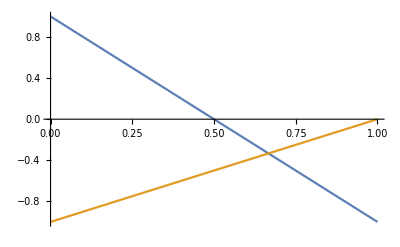

{{x→2/3,y→-1/3}}

```mathematica
f[x,y] = 2x + y == 1
g[x, y] = x - y == 1
Plot[{1 - 2x, x - 1}, {x, 0, 1}]
sol = Solve[f[x, y] && g[x, y], {x, y}]
```

```mathematica
x /. sol
y /. sol
sol // MatrixForm
sol[[1,1,2]]
sol[[1,2,2]]
```

{2/3}

{-1/3}

(x→2/3 | y→-1/3)

2/3

-1/3

```mathematica
Table[sol = Solve[{3x + y == 2, x - b y == 5}, {x, y}], {b, 1, 3}] // MatrixForm
```

((x→7/4
y→-13/4)
(x→9/7
y→-13/7)
(x→11/10
y→-13/10))

```mathematica
Table[sol = Solve[{3x + y == 2, x - b y == 5}, {x, y}]; sol[[1, 1, 2]], {b, 1, 3}] // MatrixForm
```

(7/4
9/7
11/10)

```mathematica
Solve[x == 1 && x == 2, x]
Solve[x == x, x]
```

{}

{{}}

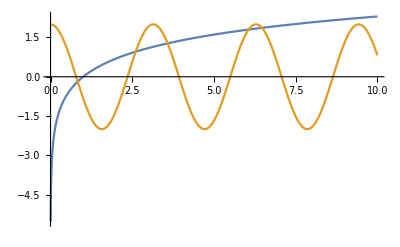

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[Log[x]==2 Cos[2 x],x]

```mathematica
Plot[{Log[x], 2 Cos[2 x]}, {x, 0, 10}]
Solve[Log[x] == 2 Cos[2x], x]
```

```mathematica
Solve[Sin[p] == 1/2, p]
Sin[π/6]
```

{{p→ConditionalExpression[π/6+2 π C[1], C[1]∈ℤ]},{p→ConditionalExpression[(5 π)/6+2 π C[1], C[1]∈ℤ]}}

1/2

```mathematica
Solve[3 x^2+2 y^2<2, {x, y}]
```

Solve::fulldim: The solution set contains a full-dimensional component; use Reduce for complete solution information.

{{}}

## FindRoot

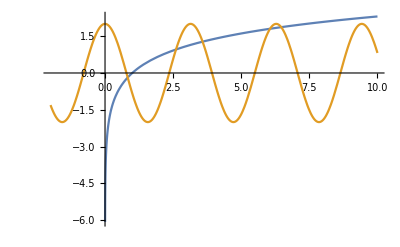

{x→6.05851}

```mathematica
Plot[{Log[x], 2 Cos[2 x]}, {x, -2, 10}]
FindRoot[Log[x] == 2Cos[2x], {x, 6}]
```

## Reduce

```mathematica
Reduce[Sin[p] == 1/2, p]
```

C[1]∈ℤ&&(p==π/6+2 π C[1]||p==(5 π)/6+2 π C[1])

```mathematica
Reduce[3 x^2 + 2 y^2 < 2, {x, y}]
```

-√(2/3)<x<√(2/3)&&-(√(2-3 x^2))/(√2)<y<(√(2-3 x^2))/(√2)

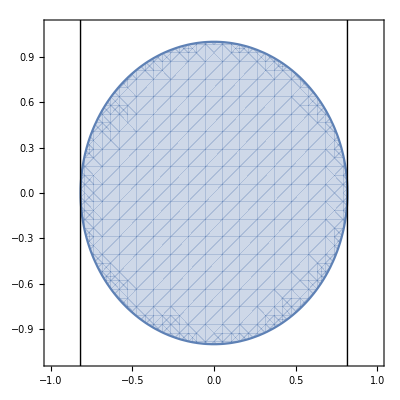

```mathematica
RegionPlot[{3 x^2+2 y^2 < 2}, {x, -1, 1}, {y, -1.1, 1.1},
Epilog -> {
    (* add vertical lines *)
    InfiniteLine[{-√(2/3), 0}, {0, 1}],
    InfiniteLine[{√(2/3), 0}, {0, 1}]
  }
]
```

## Differential Equations

## Ordinary Differential Equations

#### Solve Homogeneous Solution

```mathematica
Clear[x, y, z, a, b, c]
sol = DSolve[a y''[x] + b y'[x] + c y[x] == 0, y[x], x]
D[]
```

{{y[x]→ⅇ^(1/2 (-b/a-(√(b^2-4 a c))/a) x) C[1]+ⅇ^(1/2 (-b/a+(√(b^2-4 a c))/a) x) C[2]}}

Verify solution by plugging back into the differential equation

```mathematica
y[x_] := ⅇ^(1/2 (-b/a-(√(b^2-4 a c))/a) x) Subscript[C, 1]+ⅇ^(1/2 (-b/a+(√(b^2-4 a c))/a) x)Subscript[C, 2]
Simplify[a y''[x] + b y'[x] + c y[x]]
```

0

#### Solve Inhomogeneous Solution

```mathematica
Clear[x, y]
sol = DSolve[a y''[x] + b y'[x] + c y[x] == Cos[x], y[x], x]
```

{{y[x]→ⅇ^(1/2 (-b/a-(√(b^2-4 a c))/a) x) C[1]+ⅇ^(1/2 (-b/a+(√(b^2-4 a c))/a) x) C[2]+(-a Cos[x]+c Cos[x]+b Sin[x])/(a^2+b^2-2 a c+c^2)}}

Verify solution by plugging back into the differential equation

```mathematica
y[x_] := ⅇ^(1/2 (-b/a-(√(b^2-4 a c))/a) x) Subscript[C, 1]+ⅇ^(1/2 (-b/a+(√(b^2-4 a c))/a) x)Subscript[C, 2] +(-a Cos[x]+c Cos[x]+b Sin[x])/(a^2+b^2-2 a c+c^2)
Simplify[a y''[x] + b y'[x] + c y[x]]
```

Cos[x]

## Partial Differential Equations

```mathematica
Clear[x, y, u, sol];
equation1 = D[u[x,y], x]+x D[u[x,y], y]==Sin[x];
sol = u /. DSolve[equation1, u, {x, y}][[1]] /. Subscript[C, 1][t_] -> t
```

Function[{x,y},-Cos[x]+C[1][-x^2/2+y]]

## Boundary Conditions

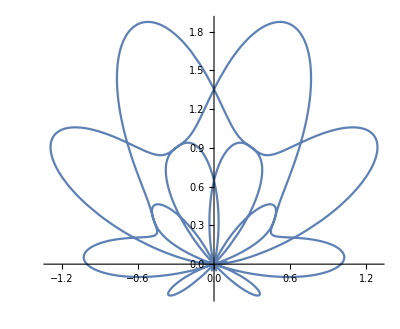

```mathematica
PolarPlot[Sin[θ]+Sin[(5θ)/2]^3, {θ, 0, 4π}]
```